```mathematica
ClearAll["Global`*"]
```

```mathematica
qq[x_,t_]=-t/v^2+x/v^4+32 t x x+16 x^5/15
```

-t/v^2+x/v^4+32 t x^2+(16 x^5)/15

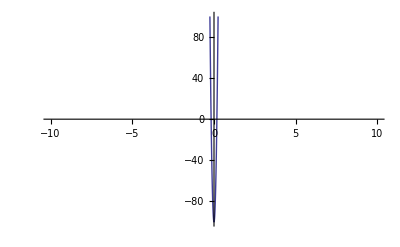

```mathematica
Plot[qq[x,100]/.v->1,{x,-10,10},PlotRange->{-100,100}]
```

```mathematica
qq1[x_,t_]=-1/v^4-(4 x^2)/v^2-16/3(12t x+x^4)-64/45 v^2(720 t^2-60 t x^3-x^6)
```

-1/v^4-(4 x^2)/v^2-16/3 (12 t x+x^4)-64/45 v^2 (720 t^2-60 t x^3-x^6)

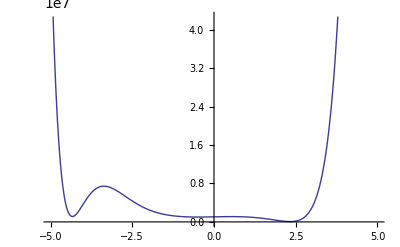

```mathematica
Plot[qq1[x,1]^2+qq[x,1]^2/.v->1,{x,-5,5}]
```

```mathematica
Plot3D[qq1[x,t]^2+qq[x,t]^2/.v->1.2,{x,-5,5},{t,-1,1},PlotRange->{0,1}]
```

-Graphics3D-

### Fully Discrete Burgers

```mathematica
qqq=(p-k)ψ[n+2]-(u[n]-u[n+2]+2p)ψ[n+1]+(p+k)ψ[n];
```

```mathematica
Series[Q[x+2 a],{a,0,3}]
```

Q[x]+2 Q'[x] a+2 Q''[x] a^2+4/3 Q^(3)[x] a^3+O[a]^4

```mathematica
qqq1=Simplify[qqq/.p->1/a/.ψ[n]->Q[x]/.u[n]->v[x]/.ψ[n+2]->Series[Q[x+2 a],{a,0,3}]]
```

(2 Q[x]-2 ψ[1+n])/a+(u[2+n] ψ[1+n]-v[x] ψ[1+n]+2 Q'[x])+(-2 k Q'[x]+2 Q''[x]) a+(-2 k Q''[x]+4/3 Q^(3)[x]) a^2+O[a]^3

```mathematica
Collect[qqq1,a]
```

(2 Q[x]-2 ψ[1+n])/a+u[2+n] ψ[1+n]-v[x] ψ[1+n]+2 Q'[x]+a (-2 k Q'[x]+2 Q''[x])+a^2 (-2 k Q''[x]+4/3 Q^(3)[x])

```mathematica
qqq1=Simplify[qqq/.p->1/a/.ψ[n]->Q[x]/.u[n]->v[x]/.ψ[n+1]->Series[Q[x+a],{a,0,3}]/.ψ[n+2]->Series[Q[x+2 a],{a,0,3}]/.u[n+2]->Series[v[x+2a],{a,0,3}]];
```

```mathematica
Collect[qqq1,a]
```

a (-2 k Q'[x]+2 Q[x] v'[x]+Q''[x])+a^2 (2 Q'[x] v'[x]-2 k Q''[x]+2 Q[x] v''[x]+Q^(3)[x])+4/3 a^3 Q[x] v^(3)[x]

```mathematica
eqq=u[n,m+1]*p-u[n+1,m]*q-(u[n,m+1]-u[n+1,m]+p-q)u[n+1,m+1];
```

```mathematica
eqq1=Simplify[eqq/.q->1/b/.u[n,m]->v[n,x]/.u[n+1,m]->v[n+1,x]/.u[n,m+1]->Series[v[n,x+b],{b,0,3}]/.u[n+1,m+1]->Series[v[n+1,x+b],{b,0,3}]];
```

```mathematica
Collect[eqq1,b]
```

(p-v[1+n,x]) (v[n,x]-v[1+n,x])+v^(0,1)[1+n,x]+b ((p-v[1+n,x]) v^(0,1)[n,x]-(p+v[n,x]-v[1+n,x]) v^(0,1)[1+n,x]+1/2 v^(0,2)[1+n,x])+b^2 (-v^(0,1)[n,x] v^(0,1)[1+n,x]+1/2 (p-v[1+n,x]) v^(0,2)[n,x]-1/2 (p+v[n,x]-v[1+n,x]) v^(0,2)[1+n,x]+1/6 v^(0,3)[1+n,x])

```mathematica
SDB=Simplify[(p-v[1+n,x]) (v[n,x]-v[1+n,x])+Derivative[0,1][v][1+n,x]]
```

(p-v[1+n,x]) (v[n,x]-v[1+n,x])+v^(0,1)[1+n,x]

This is a semi-discrete Burers:(p-v[1+n,x]) (v[n,x]-v[1+n,x])+v^(0,1)[1+n,x]

### Discrete Burgers SP

```mathematica
eq=P[n+1]+v[n]*P[n]-a*(P[n]+v[n]*P[n-1]);
```

```mathematica
eq1=Simplify[eq/.v[n]->Series[Exp[h*u[x]],{h,0,3}]/.v[n-1]->Series[Exp[h*u[x-h]],{h,0,3}]/.P[n+1]->Series[h*Q[x+h],{h,0,3}]/.P[n-1]->Series[Q[x-h]/h,{h,0,3}]/.P[n]->Q[x]/.a->1+h*b]
```

((-Q[x]/h+(-b Q[x]+Q'[x])+(-b Q[x]+b Q'[x]-Q''[x]/2) h+1/6 (-3 b Q''[x]+Q^(3)[x]) h^2+1/24 (4 b Q^(3)[x]-Q^(4)[x]) h^3+O[h]^4)+Q[x] h+Q'[x] h^2+1/2 Q''[x] h^3+O[h]^4)+(-(Q[x] u[x])/h+u[x] (Q[x]-b Q[x]+Q'[x])+u[x] (b Q'[x]-Q''[x]/2) h+1/6 u[x] (-3 b Q''[x]+Q^(3)[x]) h^2+1/24 u[x] (4 b Q^(3)[x]-Q^(4)[x]) h^3+O[h]^4) h+(-(Q[x] u[x]^2)/(2 h)+1/2 u[x]^2 (Q[x]-b Q[x]+Q'[x])+1/4 u[x]^2 (2 b Q'[x]-Q''[x]) h+1/12 u[x]^2 (-3 b Q''[x]+Q^(3)[x]) h^2+1/48 u[x]^2 (4 b Q^(3)[x]-Q^(4)[x]) h^3+O[h]^4) h^2+(-(Q[x] u[x]^3)/(6 h)+1/6 u[x]^3 (Q[x]-b Q[x]+Q'[x])+1/12 u[x]^3 (2 b Q'[x]-Q''[x]) h+1/36 u[x]^3 (-3 b Q''[x]+Q^(3)[x]) h^2+1/144 u[x]^3 (4 b Q^(3)[x]-Q^(4)[x]) h^3+O[h]^4) h^3+O[h]^4

```mathematica
Collect[eq1,h]
```

-b Q[x]-Q[x]/h-Q[x] u[x]+Q'[x]+h (Q[x]-b Q[x]+Q[x] u[x]-b Q[x] u[x]-1/2 Q[x] u[x]^2+b Q'[x]+u[x] Q'[x]-Q''[x]/2)+h^2 (1/6 (3 Q[x] u[x]^2-3 b Q[x] u[x]^2-Q[x] u[x]^3+6 Q'[x]+6 b u[x] Q'[x]+3 u[x]^2 Q'[x]-3 u[x] Q''[x])+1/6 (-3 b Q''[x]+Q^(3)[x]))+h^3 (1/12 (2 Q[x] u[x]^3-2 b Q[x] u[x]^3+6 b u[x]^2 Q'[x]+2 u[x]^3 Q'[x]+6 Q''[x]-6 b u[x] Q''[x]-3 u[x]^2 Q''[x]+2 u[x] Q^(3)[x])+1/24 (4 b Q^(3)[x]-Q^(4)[x]))